### Start choosing the example:

```mathematica
t=7;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->6}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.062901 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.088703,Null}

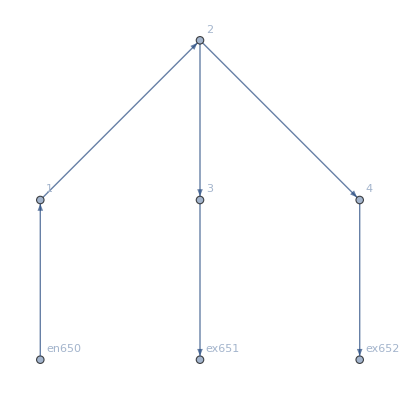

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j653→2.,j654→1.5,j655→0.5,j656→1.5,j657→0.5,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.5,jt668→0.5,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.5,jt674→0.,jt675→0.5,jt676→0.,u677→8.5,u678→6.5,u679→6.5,u680→5.,u681→6.,u682→8.5,u683→6.5,u684→5.,u685→6.,u686→5.,u687→6.,u688→8.5|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.151737

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0671729

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0284772

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0119463

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00500928

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00210191

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000882365

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000370491

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000155578

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000653338

<|j653→2.,j654→1.95976,j655→0.0402416,j656→1.95976,j657→0.0402416,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.95976,jt668→0.0402416,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.95976,jt674→0.,jt675→0.0402416,jt676→0.,u677→7.083,u678→6.03647,u679→6.03647,u680→5.,u681→6.,u682→7.083,u683→6.03647,u684→5.,u685→6.,u686→5.,u687→6.,u688→7.083|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.144815

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0612099

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0248359

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00996172

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00398705

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0015952

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000638196

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000255323

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000102147

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000408661

<|j653→2.,j654→1.91732,j655→0.082683,j656→1.91732,j657→0.082683,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.91732,jt668→0.082683,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.91732,jt674→0.,jt675→0.082683,jt676→0.,u677→7.17459,u678→6.07552,u679→6.07552,u680→5.,u681→6.,u682→7.17459,u683→6.07552,u684→5.,u685→6.,u686→5.,u687→6.,u688→7.17459|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.125314

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.047663

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171681

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00611646

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00217214

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000770603

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00027329

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000096909

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000343626

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000121843

<|j653→2.,j654→1.82868,j655→0.171318,j656→1.82868,j657→0.171318,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.82868,jt668→0.171318,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.82868,jt674→0.,jt675→0.171318,jt676→0.,u677→7.38017,u678→6.15856,u679→6.15856,u680→5.,u681→6.,u682→7.38017,u683→6.15856,u684→5.,u685→6.,u686→5.,u687→6.,u688→7.38017|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00564812

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000467942

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000383919

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.14729×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.57992×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.11482×10^-8

<|j653→2.,j654→1.54606,j655→0.453936,j656→1.54606,j657→0.453936,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.54606,jt668→0.453936,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.54606,jt674→0.,jt675→0.453936,jt676→0.,u677→8.27914,u678→6.44565,u679→6.44565,u680→5.,u681→6.,u682→8.27914,u683→6.44565,u684→5.,u685→6.,u686→5.,u687→6.,u688→8.27914|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.89724×10^-15,ComplexInfinity]

<|j653→2.,j654→1.5,j655→0.5,j656→1.5,j657→0.5,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.5,jt668→0.5,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.5,jt674→0.,jt675→0.5,jt676→0.,u677→8.5,u678→6.5,u679→6.5,u680→5.,u681→6.,u682→8.5,u683→6.5,u684→5.,u685→6.,u686→5.,u687→6.,u688→8.5|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0374283

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0078923

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00170575

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000366699

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000078923

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000016982

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.65426×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.86327×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.69203×10^-7

<|j653→2.,j654→1.41188,j655→0.588118,j656→1.41188,j657→0.588118,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.41188,jt668→0.588118,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.41188,jt674→0.,jt675→0.588118,jt676→0.,u677→9.06005,u678→6.61741,u679→6.61741,u680→5.,u681→6.,u682→9.06005,u683→6.61741,u684→5.,u685→6.,u686→5.,u687→6.,u688→9.06005|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.231364

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.168221

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.125534

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0909659

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0670511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0486281

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0356189

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0258629

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0188826

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0137221

<|j653→2.,j654→1.30174,j655→0.698262,j656→1.30174,j657→0.698262,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.30174,jt668→0.698262,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.30174,jt674→0.,jt675→0.698262,jt676→0.,u677→10.4665,u678→6.82373,u679→6.82373,u680→5.,u681→6.,u682→10.4665,u683→6.82373,u684→5.,u685→6.,u686→5.,u687→6.,u688→10.4665|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.291563

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.288145

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.285373

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.281854

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.278996

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.275386

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272449

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.268759

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.265751

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.261992

<|j653→2.,j654→1.47225,j655→0.527746,j656→1.47225,j657→0.527746,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→1.47225,jt668→0.527746,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→1.47225,jt674→0.,jt675→0.527746,jt676→0.,u677→11.2039,u678→6.85812,u679→6.85812,u680→5.,u681→6.,u682→11.2039,u683→6.85812,u684→5.,u685→6.,u686→5.,u687→6.,u688→11.2039|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.419684

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.718511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j653→2.,j654→2.,j655→0.,j656→2.,j657→0.,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→2.,jt668→0.,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→2.,jt674→0.,jt675→0.,jt676→0.,u677→13.9909,u678→7.,u679→7.,u680→5.,u681→6.,u682→13.9909,u683→7.,u684→5.,u685→2.00909,u686→5.,u687→6.,u688→13.9909|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.549253

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.805485

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j653→2.,j654→2.,j655→0.,j656→2.,j657→0.,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→2.,jt668→0.,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→2.,jt674→0.,jt675→0.,jt676→0.,u677→16.8941,u678→7.,u679→7.,u680→5.,u681→6.,u682→16.8941,u683→7.,u684→5.,u685→-0.894131,u686→5.,u687→6.,u688→16.8941|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.723085

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«16 more identical outputs»

<|j653→2.,j654→2.,j655→0.,j656→2.,j657→0.,j658→2.,j659→0.,j660→0.,j661→0.,j662→0.,j663→0.,j664→0.,jt665→0.,jt666→2.,jt667→2.,jt668→0.,jt669→0.,jt670→0.,jt671→0.,jt672→0.,jt673→2.,jt674→0.,jt675→0.,jt676→0.,u677→23.3732,u678→7.,u679→7.,u680→5.,u681→6.,u682→23.3732,u683→7.,u684→5.,u685→-7.3732,u686→5.,u687→6.,u688→23.3732|>